### Задание 8

Для задач, указанных в заданиях 5 и 7, построить двойственные задачи и показать их решение, используя уже найденные решения соответствующих прямых задач.

#### From HT 7

```mathematica
f=4 Subscript[x, 1]+6 Subscript[x, 2];
```

```mathematica
f->max;
```

```mathematica
constraints={
5 Subscript[x, 1]-2 Subscript[x, 2]-Subscript[y, 1]==10,
-2 Subscript[x, 1]+Subscript[x, 2]+Subscript[y, 2]==5,
3 Subscript[x, 2]+Subscript[y, 3]==12,
Subscript[x, 1]+Subscript[y, 4]==3
};
P={Subscript[x, 1]>=0,Subscript[x, 2]>=0,Subscript[y, 1]>=0,Subscript[y, 2]>=0,Subscript[y, 3]>=0,Subscript[y, 4]>=0};
```

```mathematica
X={Subscript[x, 1],Subscript[x, 2],Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4]};
```

```mathematica
A = D[constraints⟦All,1⟧,{X}];
A //MatrixForm
```

(5 | -2 | -1 | 0 | 0 | 0
-2 | 1 | 0 | 1 | 0 | 0
0 | 3 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1)

```mathematica
B=constraints⟦All, 2⟧
```

{10,5,12,3}

```mathematica
c = D[f, {X}]
```

{4,6,0,0,0,0}

Двойственная задача:

```mathematica
Λ=Table[Subscript[λ,i],{i,Length@B}]
```

{λ_1,λ_2,λ_3,λ_4}

```mathematica
ϕ=Λ.B
```

10 λ_1+5 λ_2+12 λ_3+3 λ_4

```mathematica
ϕ->min;
```

```mathematica
Thread[Transpose[A].Λ>=c]//TableForm
```

5 λ_1-2 λ_2+λ_4≥4
-2 λ_1+λ_2+3 λ_3≥6
-λ_1≥0
λ_2≥0
λ_3≥0
λ_4≥0

```mathematica
dualConstraints=Thread[Transpose[A].Λ>=c]/.{Subscript[λ, 1]->-Subscript[λ, 11]};
dualConstraints//TableForm
```

-2 λ_2+λ_4-5 λ_11≥4
λ_2+3 λ_3+2 λ_11≥6
λ_11≥0
λ_2≥0
λ_3≥0
λ_4≥0

Соотношения дополняющей нежёсткости:

Сделаем обратную замену {-λ_11->λ_1}

```mathematica
dualConstraints=dualConstraints/.{Subscript[λ, 11]->-Subscript[λ, 1]};
```

```mathematica
cs=Thread[X*(dualConstraints⟦All,1⟧-dualConstraints⟦All,2⟧)==0];
cs//TableForm
```

x_1 (-4+5 λ_1-2 λ_2+λ_4)==0
x_2 (-6-2 λ_1+λ_2+3 λ_3)==0
-y_1 λ_1==0
y_2 λ_2==0
y_3 λ_3==0
y_4 λ_4==0

```mathematica
optimalSolution={Subscript[x, 1]->3,Subscript[x, 2]->5/2,Subscript[y, 1]->0,Subscript[y, 2]->17/2,Subscript[y, 3]->9/2,Subscript[y, 4]->0};
f/.optimalSolution
```

27

```mathematica
Rule@@@List@@Reduce[cs/.optimalSolution,Λ]
```

{λ_1→-3,λ_2→0,λ_3→0,λ_4→19}

```mathematica
ϕ/.{Subscript[λ, 1]->-3,Subscript[λ, 2]->0,Subscript[λ, 3]->0,Subscript[λ, 4]->19}
```

27

Проверка:

```mathematica
Minimize[Prepend[dualConstraints,ϕ],Λ]
```

{27,{λ_1→-3,λ_2→0,λ_3→0,λ_4→19}}

Результат решения прямой задачи табличным симплекс-методом:

| x_1 | x_2 | y_1 | y_2 | y_3 | y_4 | СЧ
x_1 | 1 | 0 | 0 | 0 | 0 | 1 | 3
y_2 | 0 | 0 | -1/2 | 1 | 0 | -1/2 | 17/2
y_3 | 0 | 0 | -3/2 | 0 | 1 | -15/2 | 9/2
x_2 | 0 | 1 | 1/2 | 0 | 0 | 5/2 | 5/2
f | 0 | 0 | 3 | 0 | 0 | 19 | 27

#### From HT 5

Прямая задача (в стандартной форме):

```mathematica
f=-40 Subscript[x, 1]-30 Subscript[x, 2];
```

```mathematica
f->min;
```

```mathematica
X={Subscript[x, 1],Subscript[x, 2]};
```

```mathematica
constraints={
-Subscript[x, 1]-3 Subscript[x, 2]>=-15, 
-2 Subscript[x, 1]-Subscript[x, 2]>=-17,
-2 Subscript[x, 1]-3 Subscript[x, 2]>=-23
} ;
P={Subscript[x, 1]>=0,Subscript[x, 2]>=0};
```

Двойственная задача:

```mathematica
A=D[constraints⟦All,1⟧,{X}];
A//MatrixForm
```

(-1 | -3
-2 | -1
-2 | -3)

```mathematica
B=constraints⟦All,2⟧;
```

```mathematica
c=D[f,{X}]
```

{-40,-30}

```mathematica
Λ=Table[Subscript[λ,i],{i,Length@constraints}];
```

```mathematica
ϕ=constraints⟦All,2⟧.Λ
```

-15 λ_1-17 λ_2-23 λ_3

```mathematica
ϕ->max;
```

```mathematica
dualConstraints=Thread[Transpose[A].Λ<=c];
dualConstraints//TableForm
```

-λ_1-2 λ_2-2 λ_3≤-40
-3 λ_1-λ_2-3 λ_3≤-30

```mathematica
dP=Thread[Λ>=0]
```

{λ_1≥0,λ_2≥0,λ_3≥0}

Соотношения дополняющей нежёсткости:

```mathematica
cs=Thread[X*(dualConstraints⟦All,1⟧-dualConstraints⟦All,2⟧)==0];
cs//TableForm
```

x_1 (40-λ_1-2 λ_2-2 λ_3)==0
x_2 (30-3 λ_1-λ_2-3 λ_3)==0

Графическое решение прямой задачи

```mathematica
point = First@Solve[-Subscript[x, 1]-3 Subscript[x, 2]==-15&&- 2 Subscript[x, 1]-Subscript[x, 2]==-17,X]
```

{x_1→36/5,x_2→13/5}

```mathematica
minL=(-40 Subscript[x, 1]-30 Subscript[x, 2])/.point
```

-366

```mathematica
lines=Equal@@@constraints;
```

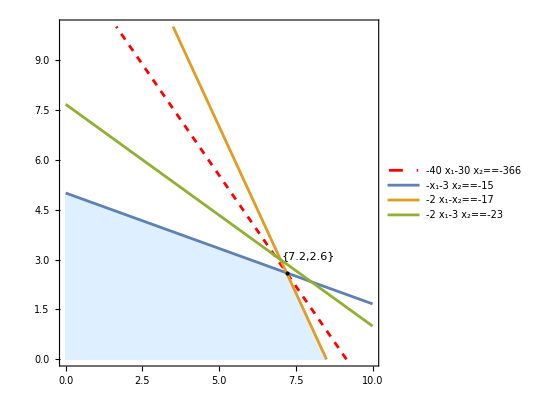

```mathematica
Show[RegionPlot[And@@Join[constraints,P],{Subscript[x, 1], 0, 10},{Subscript[x, 2], 0, 10},PlotStyle->LightBlue,BoundaryStyle->None],
ContourPlot[f==minL,{Subscript[x, 1], 0, 10},{Subscript[x, 2], 0, 10},ContourStyle->{Red,Dashed},PlotLegends->"AllExpressions"],
ContourPlot[lines,{Subscript[x, 1], 0, 10},{Subscript[x, 2], 0, 10},PlotLegends->"AllExpressions"],
Graphics[{Point[point⟦All,2⟧],Text[N@point⟦All,2⟧,point⟦All,2⟧+{0.7,0.5}]}], 
Axes->True]
```

```mathematica
dualOptimalSolution=Rule@@@List@@Reduce[cs/.Append[point,Subscript[λ, 3]->0],Λ]
```

{λ_1→4,λ_2→18}

```mathematica
ϕ/.Append[dualOptimalSolution,Subscript[λ, 3]->0]
```

-366

Проверка:

```mathematica
Maximize[Join[{ϕ},dualConstraints,dP],Λ]
```

{-366,{λ_1→4,λ_2→18,λ_3→0}}